## Exercises

For the exam complete two of these... 

Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

```mathematica
f[x_]:=Sin[x]Exp[-x]
Integrate[f[x], x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
g[x_]:=NIntegrate[f[t], {t, -5, x}]
```

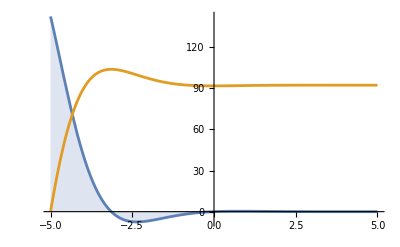

```mathematica
Plot[{f[x], g[x]}, {x,-5,5}, Filling->{1->Axis}]
```

```mathematica
D[f[x], x]
```

ⅇ^-x Cos[x]-ⅇ^-x Sin[x]

```mathematica
f'[x]
```

ⅇ^-x Cos[x]-ⅇ^-x Sin[x]

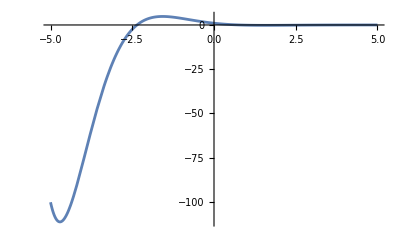

```mathematica
Plot[f'[x], {x,-5,5}]
```

Q4: Find the series expansion of the function f(x) = e^(-arctan(x)) about x=0, and about x → ∞. Hint: The arctan function is ArcTan[x].

```mathematica
Clear[f]
f[x_]:= Exp[-ArcTan[x]]
```

```mathematica
Series[f[x], {x, 0, 4}]
```

1-x+x^2/2+x^3/6-(7 x^4)/24+O[x]^5

```mathematica
Series[f[x], {x,∞, 4}]
```

ⅇ^(-π/2)+ⅇ^(-π/2)/x+ⅇ^(-π/2)/(2 x^2)-ⅇ^(-π/2)/(6 x^3)-(7 ⅇ^(-π/2))/(24 x^4)+O[1/x]^5

Q5: Solve the following differential equation using both DSolve and NDSolve (for x=-10 to x=10). Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

```mathematica
Clear[x,y]
DSolve[{y''[x] - x*y[x] == 0, y[0] == 1, y'[0] ==-3^(1/3) Gamma[2/3]/Gamma[1/3]}, y[x], x]
```

{{y[x]→3^(2/3) AiryAi[x] Gamma[2/3]}}

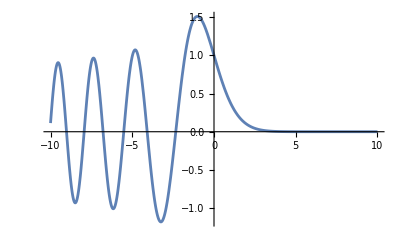

```mathematica
Plot[%[[1,1,2]], {x, -10., 10.}]
```

```mathematica
NDSolve[{y''[x] - x*y[x] == 0, y[0] == 1, y'[0] ==-(3^(1/3))* Gamma[2/3]/Gamma[1/3]},y,{x,-10,10},Method->"ImplicitRungeKutta",AccuracyGoal->13,PrecisionGoal->13,MaxSteps->Infinity]
```

{{y→InterpolatingFunction[…]}}

```mathematica
Plot[[x],{x,-10.,10.}]
```

-Graphics-